# Alcubierre warp drive single particle trajectory

## Natario metric

```mathematica
ClearAll[coordsU];
coordsU={t,r,θ,ϕ};

ClearAll[nf,f];
nf[r_]:=1/2(1-f[r]);

ClearAll[natgLL00,natgLL01,natgLL02];
natgLL00=-1+4*v^2*nf[r]^2*Cos[θ]^2+v^2*Sin[θ]^2(r*nf'[r]+2nf[r])^2;
natgLL01=-2*v*nf[r]*Cos[θ];
natgLL02=v*r(r*nf'[r]+2*nf[r]);

ClearAll[gLL];
gLL={
{natgLL00,natgLL01,natgLL02,0},
{natgLL01,1,0,0},
{natgLL02,0,r^2,0},
{0,0,0,r^2Sin[θ]^2}
};

gUU=FullSimplify[Inverse[gLL]];
```

## Particle Hamiltonian

```mathematica
ClearAll[pL];
pL={pt,pr,pθ,pϕ};

ClearAll[H];
H=1/2Sum[gUU[[a,b]]pL[[a]]pL[[b]],{a,1,4},{b,1,4}];

ClearAll[dHdpL];
dHdpL=Table[D[H,pL[[i]]],{i,1,4}];

ClearAll[dHdqU];
dHdqU=Table[D[H,coordsU[[i]]],{i,1,4}];

ClearAll[λRules,Hλ,dqUdλ,dpLdλ];
λRules={pt->pt[λ],pr->pr[λ],pθ->pθ[λ],pϕ->pϕ[λ],t->t[λ],r->r[λ],θ->θ[λ],ϕ->ϕ[λ]};
Hλ=H/.λRules;
dqUdλ=dHdpL/.λRules;
dpLdλ=-dHdqU/.λRules;

ClearAll[stateVector];
stateVector=MapThread[
Equal[#1,#2]&,
{{t'[λ],r'[λ],θ'[λ],ϕ'[λ],pt'[λ],pr'[λ],pθ'[λ],pϕ'[λ]},Join[dqUdλ,dpLdλ]}
];
```

## Hamilton’s equations integration

```mathematica
(* Metric data *)
ClearAll[r,f,v,σ,R];
v=1/2;
σ=10;
R=4;

f[r_]:=(Tanh[σ(r+R)]-Tanh[σ(r-R)])/(2Tanh[σ*R]);

(* Initial data *)
ClearAll[δ,pr0,pθ0,pϕ0,t0,r0,θ0,ϕ0];
δ=-1;

pr0=0;
pθ0=0;
pϕ0=0;

t0=0;
r0=5;
θ0=-π/2;
ϕ0=0;

ClearAll[pt0];
pt0=pt//.Solve[
Sum[
gUU[[a,b]]({pt,pr0,pθ0,pϕ0}[[a]])({pt,pr0,pθ0,pϕ0}[[b]]),
{a,1,4},
{b,1,4}
]==-1,
pt][[1]]//.{r->r0,θ->θ0,ϕ->ϕ0};

ClearAll[initialData];
initialData={t[0]==t0,r[0]==r0,θ[0]==θ0,ϕ[0]==ϕ0,pt[0]==pt0,pr[0]==pr0,pθ[0]==pθ0,pϕ[0]==pϕ0};

ClearAll[equations,variables];
equations=Join[stateVector,initialData];
variables={t,r,θ,ϕ,pt,pr,pθ,pϕ};

(* System integration *)
ClearAll[λmin,λmax];
λmin=0;
λmax=100;

ClearAll[sol];
sol=Flatten[
NDSolve[
equations,
variables,
{λ,λmin,λmax},
Method->{
"ImplicitRungeKutta",
"DifferenceOrder"->4
},
PrecisionGoal->MachinePrecision,
AccuracyGoal->MachinePrecision
]
];
```

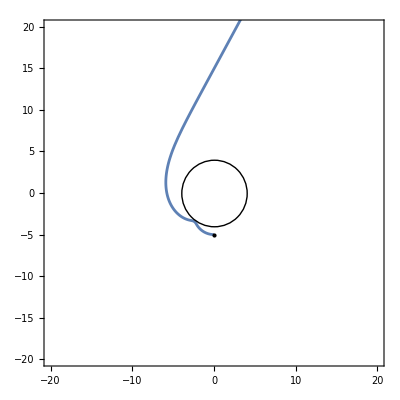

```mathematica
ParametricPlot[
{r[λ]Cos[θ[λ]],r[λ]Sin[θ[λ]]Cos[ϕ[λ]]}//.sol,
{λ,λmin,λmax},
Axes->False,
Frame->True,
AspectRatio->1,
PlotRange->{{-20,20},{-20,20}},
Epilog->{
Circle[{0,0},R],
Point[{{r[0]Cos[θ[0]]//.sol,r[0]Sin[θ[0]]//.sol}}]
}
]
```